```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
```

```mathematica
DeclareIndexFlavor[{dotted,Orange}]
DeclareIndexFlavor[{undotted,Blue}]
Clear[tu,td]
DefineTensorShortcuts[{{η,v,D,F,Λ,H,R,τ,μ,u,Y,Γ,Q,d,L,Z,W,λ,T,t,M,ν,S,C,U,m},1},
{{m,G,b,u,H,Q,e,ν},2},
{{σ,ξ,y,a,u,Q,y},3}
]
AddBaseIndex[{dotted,{1,2}}];
AddBaseIndex[{undotted,{1,2}}];
Put[SaveFile=NBname["stub"]<>".out"]
```

```mathematica
PR1["Neutrino mass.  Very small m_ν->1/30 [eV] or m_ν/v ∼ 10^-13. 
The difference in {ν_L-ν_R} mass spectrum could be the seesaw mechanism where the neutrino lagrangian is ",
Subscript[ℒ, ν]->l.yd[ν].νu[c].h+Mdd[i,j].νud[c,i].νd[i]
]
```

Neutrino mass.  Very small m_ν->1/30 [eV] or m_ν/v ∼ 10^-13. 
The difference in {ν_L-ν_R} mass spectrum could be the seesaw mechanism where the neutrino lagrangian is ℒ_ν→M_ij^ij.ν_ci^ci.ν_i^i+l.y_ν^ν.ν_c^c.h

```mathematica
PR1[CG["From: http://www.fynu.ucl.ac.be/librairie/theses/gustaaf.brooijmans/node14.html"],Yield,
"SeeSaw mechanism for neutrino mass terms with Lagrangian term",
tmpL=Subscript[ℒ, mass]->(tmp=-1/2 MatrixForm[{{OverBar[νd[L]],OverBar[νdu[R,c]]}}].ℳ.MatrixForm[{{νdu[L,c]},{νd[R]}}])+SuperDagger[tmp],
" where ",
sub=ℳ->MatrixForm[{{mdd[L,M],md[D]},{md[D],mdd[R,M]}}],Yield,
tmpL=tmpL/.sub,
"POFF",
NL,"We find basis where mass matrix is diagonal with diagonal elements ",
tmp=Eigenvalues[sub[[2,1]]],Yield,
tmp=tmp/.{mdd[L,M]->ad mdd[R,M],md[D]->bd mdd[R,M]}//Simplify,Yield,
tmp=Series[PowerExpand[tmp],{ad,0,2},{bd,0,2}]//Normal,Yield,
tmp=tmp/.ad->a/mdd[R,M]/.bd->b/mdd[R,M]//Expand,Yield,
tmp=tmp/.a_/mdd[R,M]^2->0/.a_/mdd[R,M]^3->0/.a->mdd[L,M]/.b->md[D],
"PON",
NL,"We have situation where the mass of one particle is ",tmp[[2]]," and can be very heavy and ",tmp[[1]]," is very light by assuming ",mdd[L,M]->0,and,mdd[R,M]≫md[D]
]
```

From: http://www.fynu.ucl.ac.be/librairie/theses/gustaaf.brooijmans/node14.html
→ SeeSaw mechanism for neutrino mass terms with Lagrangian termℒ_mass→-1/2 (OverBar[ν_L^L] | OverBar[ν_Rc^Rc]).ℳ.(ν_Lc^Lc
ν_R^R)+(-1/2 (OverBar[ν_L^L] | OverBar[ν_Rc^Rc]).ℳ.(ν_Lc^Lc
ν_R^R))^† where ℳ→(m_LM^LM | m_D^D
m_D^D | m_RM^RM)
→ ℒ_mass→-1/2 (OverBar[ν_L^L] | OverBar[ν_Rc^Rc]).(m_LM^LM | m_D^D
m_D^D | m_RM^RM).(ν_Lc^Lc
ν_R^R)+(-1/2 (OverBar[ν_L^L] | OverBar[ν_Rc^Rc]).(m_LM^LM | m_D^D
m_D^D | m_RM^RM).(ν_Lc^Lc
ν_R^R))^†
We have situation where the mass of one particle is ((m_D^D)^2)/m_RM^RM+m_RM^RM and can be very heavy and m_LM^LM-((m_D^D)^2)/m_RM^RM is very light by assuming m_LM^LM→0 and m_RM^RM≫m_D^D

```mathematica
PR1["Neutrino mass generated seesaw mechanism and as a means to produce lepton asymmetry.  A simple Lagrangian that may produce n - n̄ ≠ 0: ",
Subscript[ℒ, ν]->(tmp=l.yd[i].nd[i].h + nd[i]. (Mdd[i,j]/2).nd[j])+SuperDagger[tmp],
" where ",
{l->{"2-component lepton field ",{{OverBar[νd[L]],OverBar[ed[L]]}}},
yd[i]->"interaction matrix",
nd[i]->"neutrino field",
h->"Higg boson",
Mdd[i,j]->"neutrino mass matrix"
}//Column
]
```

Neutrino mass generated seesaw mechanism and as a means to produce lepton asymmetry.  A simple Lagrangian that may produce n - n̄ ≠ 0: ℒ_ν→n_i^i.M_ij^ij/2.n_j^j+l.y_i^i.n_i^i.h+(n_i^i.M_ij^ij/2.n_j^j+l.y_i^i.n_i^i.h)^† where l→{2-component lepton field ,{{OverBar[ν_L^L],OverBar[e_L^L]}}}
y_i^i→interaction matrix
n_i^i→neutrino field
h→Higg boson
M_ij^ij→neutrino mass matrix

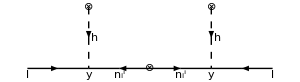
We have diagram
-Graphics-

```mathematica
PR1["We have diagram",
NL,Graphics[{{MidArrow[{{0,0},{1,0}}],MidArrow[{{2,0},{1,0}}],Dashed,MidArrow[{{1,1},{1,0}}]},{MidArrow[{{2,0},{3,0}}],MidArrow[{{4,0},{3,0}}],Dashed,MidArrow[{{3,1},{3,0}}]},Inset[y,{1,-.1}],Inset[l,{0,-.1}],
Inset[nd[i],{1.5,-.1}],Inset[nd[i],{2.5,-.1}],
Inset[y,{3,-.1}],Inset[l,{4,-.1}],Inset[h,{1.1,.5}],Inset[h,{3.1,.5}],Inset["⊗",{2,0}],Inset["⊗",{1,1}],Inset["⊗",{3,1}]},
ImageSize->300
]
]
```

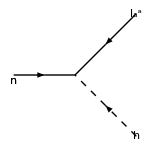
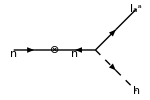
We look for difference in decay rates between the processes: 
{-Graphics-,-Graphics-}
{n→h̄ l̄,n→h l}

```mathematica
PR1["We look for difference in decay rates between the processes: ",NL,
{
Graphics[{Arrowheads[.1],MidArrow[{{0,0},{1,0}}],MidArrow[{{2,1},{1,0}}],Dashed,MidArrow[{{2,-1},{1,0}}],Inset[n,{0,-.1}],Inset[n,{0,-.1}],Inset[h,{2,-1}],Inset[ld[a],{2,1}]},ImageSize->150],
Graphics[{Arrowheads[.1],MidArrow[{{-1,0},{0,0}}],MidArrow[{{1,0},{0,0}}],MidArrow[{{1,0},{2,1}}],Dashed,MidArrow[{{1,0},{2,-1}}],Inset[n,{-1,-.1}],Inset[h,{2,-1}],Inset[ld[a],{2,1}],Inset["⊗",{0,0}],Inset["n",{.5,-.1}]},ImageSize->150]
},
NL,
{n->l̄ h̄,n->l h}
]
```

```mathematica
PR1["Overview of leptogenesis -> baryongenisis.
Factors:
1. Production of n <- {Y_n[initial],extra gauge interaction}
2. ΔΓ <- Γ - Γ̄
3. Washout
4. B+L anomoly "
]
```

Overview of leptogenesis -> baryongenisis.
Factors:
1. Production of n <- {Y_n[initial],extra gauge interaction}
2. ΔΓ <- Γ - Γ̄
3. Washout
4. B+L anomoly

```mathematica
PR1["Investigate ΔΓ which contributes to asymmetry",
Yd[B]->(28/51).xSum[Yd[nd[i][initial]],{i∈flavor}].fd[i][Therm.eq].(ΔΓ/Γ).W[ashout][i],

]
```

Investigate ΔΓ which contributes to asymmetryY_B^B→28/51.UnderBar[∑]_{i∈flavor}[Y_(n_i^i[initial])^(n_i^i[initial])].fd[i][Therm.eq].ΔΓ/Γ.W[ashout][i]Null